### Code

#### Code for sessies

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

#### Code to display and evaluate/expand normal and indexed concatenation

```mathematica
Concatenate[l__List] := Join[l];
Format[Concatenate[l__]] := Row[Riffle[{l},"⧺"]];  (* FromCharacterCode[10746] *)
```

```mathematica
Clear[IndexedConcatenate];
Format[IndexedConcatenate[x__, {var_, start_, finish_}]] :=
DisplayForm[RowBox[{UnderoverscriptBox["€", RowBox[{var,"⊨", start}], finish], "[", Sequence @@ Riffle[{x}, ","], "]"}]];  (* FromCharacterCode[8364] *)
Format[IndexedConcatenate[x__, {var_, finish_}]] :=  DisplayForm[RowBox[{UnderoverscriptBox["€", var, finish], "[", Sequence @@ Riffle[{x}, ","], "]"}]];
Format[IndexedConcatenate[x__, finish_]] := DisplayForm[RowBox[{OverscriptBox["€", finish], "[", Sequence @@ Riffle[{x}, ","], "]"}]];
```

```mathematica
iC[x__, iter:(_Integer|{_,_Integer}|{_,_Integer,_Integer})]:= Sequence @@ (Join @@ Table[{x},  iter]); 
(* allow 1 or more elements to be repeated & concatenated according to iter, result will be a subsequence, assumed to be inside a List *)
iC[x__] := IndexedConcatenate[x] (* any non-resolved cases redefined, awaiting further processing *)

Unprotect[Expand,ExpandAll];
ExpandAll[x_ /; !FreeQ[x,IndexedConcatenate]] := (x //. IndexedConcatenate->iC);
Expand[x_ /; !FreeQ[x,IndexedConcatenate] ] := (x /. IndexedConcatenate->iC);
Protect[Expand,ExpandAll];
```

#### Code to convert a network to/from its specification as a list of sets of integers, and compact it

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
```

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

#### Code to (attempt to) reduce lists to (nested) indexed concatenations

```mathematica
$debug=False;
```

```mathematica
ReduceSetList::usage ="ReduceSetList[l] takes a list l of elements or nested lists of elements, and summarizes duplicate elements and duplicate subsequences using DoConcatenate objects, having the format €_(var=start)^finish[...], specifying how many times the elements or subsequences are repeated.";
```

```mathematica
Clear[FindSeqFns];
FindSeqFns[repLen_Integer,varName_,subseqList_List] := Module[{parted,firstRep,numArray,fnList,ans},
If[$debug && "N"===Input["Continue? (Y/N)"],Abort[]];
parted=Partition[subseqList,repLen];
firstRep=First@parted;
If[$debug,Print["Entering FindSeqFns with:\n parted: ",parted,"\n firstRep: ",firstRep]];
numArray = Transpose[Cases[#,_Integer,∞]& /@ parted];
If[$debug,Print["\nNumerical Table to fit:\n",Grid@Transpose@numArray]];
fnList=FindSequenceFunction[#,varName]& /@ numArray;

If[$debug,Print["Function list: ",fnList];  Print[parted, " : ",firstRep];  Print@Position[firstRep,_Integer]; 
Print[ReplacePart[firstRep,Thread[Position[firstRep,_Integer] -> fnList]]]];
ans={IndexedConcatenate[Sequence@@ReplacePart[firstRep,Thread[Position[firstRep,_Integer] -> fnList]],{varName,1,Length[subseqList]/repLen}]};
If[$debug,
Print["ans: ",ans]; 
Print["ExpandAll[ans]: ",ExpandAll[ans]]; 
Print["ExpandAll[subseqList]: ",ExpandAll[subseqList]];
Print@If[ExpandAll[ans]===ExpandAll[subseqList],"(same)","(different)"]
];

If[ExpandAll[ans]===ExpandAll[subseqList],ans,subseqList]
];
```

```mathematica
improveReduction[l_List] := Module[{l1=l,l0=l,p},
If[$debug && "N"===Input["Continue? (Y/N)"],Abort[]];

If[$debug,Print["Entering improveReduction with: ",l]];
If[Length[l]<=1,
If[$debug,Print["Immediate Return"]];
Return[l]
];
p=Flatten@Position[l0,IndexedConcatenate[__,{__}],{1}]; (* find parts that might allow improved reduction *)
(* this only fits indexed concatenate objects with iterators in {...} *)
While[Length[p]>0 && Length[l0]>1,
If[$debug,Print["Trying to improve reduction at pos: ",First[p], " (of ",p,")\nLength[p] = ",Length[p],", Length[l0] = ",Length[l0]]];
l1=improveReductionAt[First[p],l0];
 (* try reducing based on (pos of) first DoConcatentate object *)
If[l1===l0, (* nothing changed, that didn't help *)
p=Rest[p], (* drop first location, try next *)
If[$debug,Print["improvement (p was ",p,"): ",l1]];
l0=l1; p=Flatten@Position[l0,IndexedConcatenate[__,{__}],{1}]; (* if improved, restart from top *)
]; (* end If *)
]; (* end While *)
l1  (* this is now the best we can do *)
];
```

```mathematica
improveReductionAt[k_Integer,l_List] :=
(* Assuming that there is a IndexedConcatenate object at position k in l, "roll" the contents to check that it can actually apply to elements immediately to its left, continuing until it fails. This should pick up cases like €^0[___], which can't be identified otherwise. *) 
Module[{wholeL,leftL,midEl,rightL,leftLNew,midElNew,rightLNew,leftEltsToDrop,temp,countRolled=0,rollLen,oldArgList,newArgList,iter,iterVar,iterStart,iterStop},
If[k<1||k>Length[l],Print["Error using k=",k,", l=",l];Abort[]];
wholeL=ExpandAll@l;
leftL= Take[l,k-1];                       (* l[[;;k-1]] *)
midEl=l[[k]];
rightL=Drop[l, k];                    (* l[[k+1;;]] *)

If[Head[midEl]=!=IndexedConcatenate,Print["Error: improveReduction called erroneously!"];Break[]
];

While[
(* we'll RollRight the midEl arguments before the iterator, drop the last elt of leftL, prepend an elt to rightL, check against wholeL, and track the countRolled. *)

If[$debug,Print["Before roll attempt: ",wholeL]];

If[Length[leftL]==0,
If[$debug,Print["No further rolling possible, we're at beginning"]];
Break[] (* out of this While loop *)
];
leftLNew =leftL;

oldArgList = Most[List@@midEl];
iter = Last[List@@midEl];
If[Length[iter]==2,iterStart=1,(* if 3 *) iterStart=iter[[2]]];
iterVar=First[iter];
iterStop=Last[iter];

newArgList = RotateRight[oldArgList];  (* roll arg list *)newArgList[[1]] = (newArgList[[1]] /. iter[[1]] ->iter[[1]]-1); (* adj 1st *)
newArgList=FullSimplify[newArgList];

If[$debug,Print["oldArgList: ",oldArgList]];
If[$debug,Print["iter: ",iter," : \n iterVar = ",iterVar,"\n iterStart = ",iterStart,"\n iterStop = ",iterStop]];
If[$debug,Print["newArgList: ",newArgList]];

leftEltsToDrop = ExpandAll@{First[newArgList] /. iterVar -> iterStart};

If[$debug,Print["leftEltsToDrop: ",leftEltsToDrop]];

While[ (* condition is whether we can shift the midEl one space to the left or not giving the same result *)
Length[leftEltsToDrop]>0 && Length[leftLNew]>0 &&
Length[(temp={ExpandAll[Last[leftLNew]]})] <= Length[leftEltsToDrop], 
If[$debug,Print["old value of leftLNew: ",leftLNew]];
leftLNew=Most[leftLNew];                                                                (* drop one term from the leftLNew *)
If[$debug,Print["new value of leftLNew: ",leftLNew]];
If[$debug,Print["dropping last ",Length[temp]," element(s) from leftEltsToDrop: ",leftEltsToDrop]];
leftEltsToDrop = Drop[leftEltsToDrop,-Length[temp]]; 
(* drop the right number of elements from (expanded) list *)
If[$debug,Print["new leftEltsToDrop: ",leftEltsToDrop]];
];
midElNew= IndexedConcatenate[Sequence@@newArgList, iter];
rightLNew = Prepend[rightL,(Last[oldArgList] /. iterVar ->iterStop)]; (* adj 1st *)

countRolled++; (* how many times did we successfully "roll" it? *)

If[$debug,Print["leftLNew: ",leftLNew,"\nMidElNew: ",midElNew,"\nrightLNew: ",rightLNew,"\n"]];
(* note that midElNew is just the element IndexedConcatenate, not a subsequence! *)
If[$debug,Print["countRolled: ",countRolled,"\n"]];

If[$debug,
If[wholeL=!=ExpandAll[Join[leftLNew ,{midElNew},rightLNew]],
Print["roll gives different result: "];
Print["wholeL: ",wholeL];
Print["leftLNew: ",leftLNew,"\nMidElNew: ",midElNew,"\nrightLNew: ",rightLNew];
Print["new stuff: ",Join[leftLNew ,{midElNew},rightLNew]];
Print["ExpandAll[new stuff]: ",ExpandAll[Join[leftLNew ,{midElNew},rightLNew]]],
Print["roll gives same result"]
]
];
wholeL===ExpandAll[Join[leftLNew ,{midElNew},rightLNew]], 
(* While condition, if it worked, try it again! *)
leftL=leftLNew;
midEl=midElNew;
rightL=rightLNew
];
(* We drop out of the While when the Roll didn't work, so our best answer is: *)
countRolled--; (* back off the count, and we'll use previous leftL, midEl, rightL *)

If[$debug,Print["Farthest left: ",Join[leftL,{midEl},rightL]]];

(* Now find how many elements we can drop from rightL if the index max is increased *)
 
midElNew=midEl;      (* revert, last roll didn't work *)
rightLNew=rightL;   (* revert both *)
newArgList = oldArgList = Most[List@@midEl]; (* revert arg list, too! *)

If[countRolled>=(rollLen=Length[newArgList]),  (* length of indexed subsequence *)
iterStop+=Quotient[countRolled,rollLen];  (* incr iterStop *)
midElNew= IndexedConcatenate[Sequence@@newArgList, {iterVar,iterStart,iterStop}];
(* change index max by # full subseqs *)
If[$debug,Print["dropping ",rollLen * Quotient[countRolled,rollLen]," elements from rightLNew: ",rightLNew]];
rightLNew=Drop[rightLNew,rollLen * Quotient[countRolled,rollLen]];  (* drop any full subsequences *)
countRolled -= rollLen * Quotient[countRolled,rollLen];
];
If[$debug,
Print["countRolled: ",countRolled];
Print["midElNew: ",midElNew];
Print["rightLNew: ",rightLNew]
];

rightLNew = SequenceReplace[rightLNew, {IndexedConcatenate[a_,iter1_], IndexedConcatenate[a_,iter2_]}:>
Which[
Head[iter1]===Head[iter2]===Integer, (* reps, no varName *)
List@IndexedConcatenate[a,iter1+iter2],
Head[iter1]===Integer && MatchQ[iter2,{varName_,__Integer}],
List@IndexedConcatenate[a,iter2[[;;-2]] ~Join~ iter2[[3]]+iter1],
Head[iter2]===Integer && MatchQ[iter1,{varName_,__Integer}],
List@IndexedConcatenate[a,iter1[[;;-2]] ~Join~ iter1[[3]]+iter2],
True,
{IndexedConcatenate[a,iter1], IndexedConcatenate[a,iter2]} (* no help! *)
]
]; (* merge neighbors if... *)

If[$debug,
Print["countRolled: ",countRolled];
Print["rightLNew: ",rightLNew]
];

(* check whether we might still have a subsequence from pieces left in rightL *)

While[ (* length possible and it matches *)
rollLen<=Length[rightLNew] && 
(temp=(newArgList /. iterVar-> iterStop+1))===rightLNew[[;;Length[temp]]],
iterStop++;
If[$debug,Print["incrementing iterStop: ", iterStop]];
midElNew= IndexedConcatenate[Sequence@@newArgList, {iterVar,iterStart,iterStop}];
If[$debug,Print["dropping ",rollLen," elements from rightLNew: ",rightLNew]];
rightLNew=Drop[rightLNew,rollLen]; (* drop one subseq from rightLNew *)
];

If[$debug,
Print["midElNew: ",midElNew];
Print["rightLNew: ",rightLNew];
];

Join[leftL,{midElNew},rightLNew]  (* leftL won't have changed, but maybe midElNew & rightLNew have *)
];
```

```mathematica
ReduceSetList[l_List]:=Module[{l1,l0=l,gl0,repLen,repMax,pos,varName,i,x,p,len},
If[$debug && "N"===Input["Continue? (Y/N)"],Abort[]];

If[$debug,Print["Entering ReduceSetList with: ",l]];
If[Length[l]<=1,
If[$debug,Print["Immediate Return"]];
Return[l]
];

(* first check for subsequences of duplicate elements *)

len=Length[l0];
l1=SequenceReplace[l0,
{x:Repeated[a_,{2,len}]}:>IndexedConcatenate[a,Length[{x}]]
]; (* looks for an exactly repeated subsequence *)

If[l1 =!= l0,(* not same, repLen 1 worked *)
If[$debug,Print["exact repLen = 1: ",l1]];
l1=improveReduction[l1];
If[$debug,Print["improved? : ",l1]];
l1=ReduceSetList[l1];
Return[l1]; 
(* if changed, call recursively to continue trying *)
];

If[$debug,Print["exact repLen: ",1]]; (* report what we tried *)
repLen = 2; (* start with length of repeating unit = 2, up to max useful *)
l0=l1; (* set up to check next attempted reduction *)
While[2 repLen <= (len=Length[l1]),
If[$debug,Print["exact repLen: ",repLen]];
l1=SequenceReplace[l1,
{x:Repeated[PatternSequence@@Table[ToExpression[ToString@Unique[x]<>"_"],{repLen}],{2,∞}]}:>
IndexedConcatenate[Sequence@@Take[{x},repLen],Length[{x}]/repLen]
];
If[l1 =!= l0,
If[$debug,Print["Changed (in While): exact repLen = ",repLen,": ",l1]];
l1=improveReduction[l1];
If[$debug,Print["improved? : ",l1]];
l1=ReduceSetList[l1];
If[$debug,Print["reduced? : ",l1]];
Return[l1]
];
(* if changed, call recursively to continue reduction, else try next repLen *)
repLen++;
];
If[$debug,Print["Exiting While[...replen...]"]];

If[l1 =!= l0,
If[$debug,Print["Changed: exact repLen = ",repLen,": ",l1]];
l1=improveReduction[l1];
If[$debug,Print["improved? : ",l1]];
l1=ReduceSetList[l1];
If[$debug,Print["reduced? : ",l1]];
Return[l1]
];(* if changed, call recursively to continue trying, else try the generic list *)

If[$debug,Print["Treating Generic patterns"]];

repLen = 1;            (* first time choice *)
l0={};                     (* force one time through loop *)

While[l1=!=l0 && Length[l1]>1, (* while changed, and of course, the first time *)
l0=l1;
If[$debug,Print["orig: ",l0]];
len=Length[l0];

gl0=(l0 /. (i_Integer /; i!=1) ->0);

If[$debug,Print["generic: ",gl0]];

pos=SequencePosition[gl0,{Repeated[PatternSequence[x_],{2,len}]},Overlaps->False];
If[$debug,Print["generic repLen: ", repLen,", pos: ",pos]];

While[Length[pos]==0 && Length[l0]>1 &&Length[l0]>2*(repLen+1),
repLen++;
pos=SequencePosition[gl0,{Repeated[PatternSequence@@Table[ToExpression[ToString@Unique[x]<>"_"],{repLen}],{2,∞}]},Overlaps->False];
If[$debug,Print["generic repLen: ", repLen,", pos: ",pos]];
];

If[pos==0,
If[$debug,Print["Returning, no generic matches found"]];
Return[l0]];  (* No further reduction found *)

(* at least one possible reduction found *)

Do[     (* find first unused variable name of form n$i, where i is an integer *)
varName=ToExpression["n$"<>ToString[i]];
If[FreeQ[l0,varName],Break[]],
{i,1,∞}];

If[$debug,Print["new varName: ",varName]];

l1=Flatten[SequenceSplit[l0,Thread[(Take[l0,#]& /@ pos) -> (FindSeqFns[repLen,varName,Take[l0,#]]& /@ pos)]],1];
If[l1=!=l0, 
If[$debug,Print["generic repLen = ",repLen,": ",l1]];
l1=improveReduction[l1];
If[$debug,Print["improved? : ",l1]];
];
]; (* end of While l1≠l0 loop *)

l1 (* here l1==l0, best we can do *)
];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs01=FromReducedRankIndex[253518005]
```

<|Index→253518005,QCode→343233422343,RuleSet→{ABA→AAB,A→ABA}|>

We can pull out the ruleset itself:

```mathematica
rs01[["RuleSet"]]
```

{ABA→AAB,A→ABA}

Or start from a ruleset:

```mathematica
rs02=FromReducedRankRuleSet[{"AA"->"","AB"->"BA","A"->"BB","B"->"AAA"}]
```

<|Index→702927424475,QCode→31342432243424233,RuleSet→{AA→,AB→BA,A→BB,B→AAA}|>

We generate the sessie and its causal network, again giving it a convenient name:



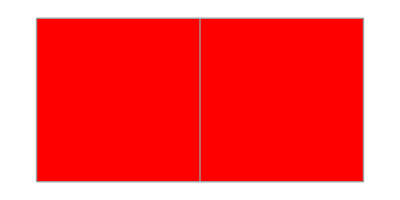

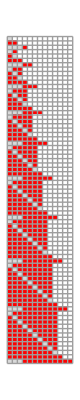
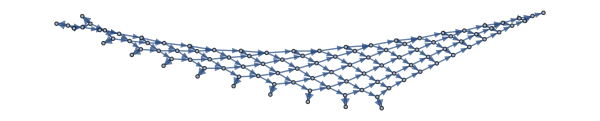
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss02=SSS[rs02[["RuleSet"]], "A",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss02[["Net"]]//Short
```

{1→2,2→3,2→3,2→4,1→4,4→5,4→6,6→7,6→7,6→8,5→8,«728»,395→396,370→396,396→397,371→397,397→398,372→398,398→399,373→399,399→400,373→400}

```mathematica
nds02=ToNetDifferenceSets[sss02[["Net"]]]
```

{{1,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},{1,3},{1,4},{4,5},{1,1,2},{},{1,4},{1,5},{1,5},{5,6},{1,1,2},{},{1,5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{},{1,6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{},{1,7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{},{1,8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{},{1,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{},{1,10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{},{1,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{},{1,12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{},{1,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,1,2},{},{1,14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15,16},{1,1,2},{},{1,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,17},{1,1,2},{},{1,16},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17,18},{1,1,2},{},{1,17},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,19},{1,1,2},{},{1,18},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19,20},{1,1,2},{},{1,19},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,21},{1,1,2},{},{1,20},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21,22},{1,1,2},{},{1,21},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22,23},{1,1,2},{},{1,22},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{23,24},{1,1,2},{},{1,23},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,25},{1,1,2},{},{1,24},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{25,26},{1,1,2},{},{1,25},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{26,27},{1,1,2},{},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds02,27]
```

{{373,2}}

```mathematica
nds02[[1;;373]]
```

{{1,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},{1,3},{1,4},{4,5},{1,1,2},{},{1,4},{1,5},{1,5},{5,6},{1,1,2},{},{1,5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{},{1,6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{},{1,7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{},{1,8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{},{1,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{},{1,10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{},{1,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{},{1,12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{},{1,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,1,2},{},{1,14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15,16},{1,1,2},{},{1,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,17},{1,1,2},{},{1,16},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17,18},{1,1,2},{},{1,17},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,19},{1,1,2},{},{1,18},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19,20},{1,1,2},{},{1,19},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,21},{1,1,2},{},{1,20},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21,22},{1,1,2},{},{1,21},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22,23},{1,1,2},{},{1,22},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{23,24},{1,1,2},{},{1,23},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,25},{1,1,2},{},{1,24},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{25,26},{1,1,2},{},{1,25},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{26,27}}

Try the reduction:

```mathematica
rsl02=ReduceSetList[nds02[[1;;373]]]
```

{{1,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},€_(n$1⊨1)^2[{1,2+n$1}],€_(n$2⊨1)^22[{3+n$2,4+n$2},{1,1,2},{},{1,3+n$2},€^(1+n$2)[{1,4+n$2}]],{26,27}}

The most compressed part is

```mathematica
rsl02[[9]]
```

€_(n$2⊨1)^22[{3+n$2,4+n$2},{1,1,2},{},{1,3+n$2},€^(1+n$2)[{1,4+n$2}]]

```mathematica
rsl02[[9]]//InputForm
```

IndexedConcatenate[{3 + n$2, 4 + n$2}, {1, 1, 2}, {}, {1, 3 + n$2}, IndexedConcatenate[{1, 4 + n$2}, 1 + n$2], {n$2, 1, 22}]

Start it earlier, stop it whenever you want:

```mathematica
IndexedConcatenate[{3 + n$2, 4 + n$2}, {1, 1, 2}, {}, {1, 3 + n$2}, IndexedConcatenate[{1, 4 + n$2}, 1 + n$2], {n$2, -2, 15}]/.n$2->k
```

€_(k⊨-2)^15[{k+3,k+4},{1,1,2},{},{1,k+3},€^(k+1)[{1,k+4}]]

This is the same thing as

```mathematica
IndexedConcatenate[{n$2, n$2+1}, {1, 1, 2}, {}, {1, n$2}, IndexedConcatenate[{1, n$2+1}, n$2-2], {n$2, 1, 15}]/.n$2->k
```

€_(k⊨1)^15[{k,k+1},{1,1,2},{},{1,k},€^(k-2)[{1,k+1}]]

```mathematica
{ExpandAll[%]}
```

{{1,2},{1,1,2},{},{1,1},{2,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},{1,3},{1,4},{4,5},{1,1,2},{},{1,4},{1,5},{1,5},{5,6},{1,1,2},{},{1,5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{},{1,6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{},{1,7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{},{1,8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{},{1,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{},{1,10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{},{1,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{},{1,12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{},{1,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,1,2},{},{1,14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15,16},{1,1,2},{},{1,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16}}

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```

-Graphics-

#### Two Linear (1D) examples

```mathematica
FromReducedRankIndex[2]
```

<|Index→2,QCode→0,RuleSet→{A→,→A}|>

By the way, look at these patterns in the Reduced Rank Enumeration for SSSs:

```mathematica
FromReducedRankIndex /@ Range[50]//Column
```

<|Index→1,QCode→,RuleSet→{A→}|>
<|Index→2,QCode→0,RuleSet→{A→,→A}|>
<|Index→3,QCode→1,RuleSet→{A→,A→}|>
<|Index→4,QCode→2,RuleSet→{A→A}|>
<|Index→5,QCode→3,RuleSet→{AA→}|>
<|Index→6,QCode→4,RuleSet→{B→}|>
<|Index→7,QCode→00,RuleSet→{A→,→A,→,A→}|>
<|Index→8,QCode→01,RuleSet→{A→,→A,→A}|>
<|Index→9,QCode→02,RuleSet→{A→,→A,A→}|>
<|Index→10,QCode→03,RuleSet→{A→,→AA}|>
<|Index→11,QCode→04,RuleSet→{A→,→B}|>
<|Index→12,QCode→10,RuleSet→{A→,A→,→A}|>
<|Index→13,QCode→11,RuleSet→{A→,A→,A→}|>
<|Index→14,QCode→12,RuleSet→{A→,A→A}|>
<|Index→15,QCode→13,RuleSet→{A→,AA→}|>
<|Index→16,QCode→14,RuleSet→{A→,B→}|>
<|Index→17,QCode→20,RuleSet→{A→A,→,A→}|>
<|Index→18,QCode→21,RuleSet→{A→A,→A}|>
<|Index→19,QCode→22,RuleSet→{A→A,A→}|>
<|Index→20,QCode→23,RuleSet→{A→AA}|>
<|Index→21,QCode→24,RuleSet→{A→B}|>
<|Index→22,QCode→30,RuleSet→{AA→,→A}|>
<|Index→23,QCode→31,RuleSet→{AA→,A→}|>
<|Index→24,QCode→32,RuleSet→{AA→A}|>
<|Index→25,QCode→33,RuleSet→{AAA→}|>
<|Index→26,QCode→34,RuleSet→{AB→}|>
<|Index→27,QCode→40,RuleSet→{B→,→A}|>
<|Index→28,QCode→41,RuleSet→{B→,A→}|>
<|Index→29,QCode→42,RuleSet→{B→A}|>
<|Index→30,QCode→43,RuleSet→{BA→}|>
<|Index→31,QCode→44,RuleSet→{C→}|>
<|Index→32,QCode→000,RuleSet→{A→,→A,→,A→,→A}|>
<|Index→33,QCode→001,RuleSet→{A→,→A,→,A→,A→}|>
<|Index→34,QCode→002,RuleSet→{A→,→A,→,A→A}|>
<|Index→35,QCode→003,RuleSet→{A→,→A,→,AA→}|>
<|Index→36,QCode→004,RuleSet→{A→,→A,→,B→}|>
<|Index→37,QCode→010,RuleSet→{A→,→A,→A,→,A→}|>
<|Index→38,QCode→011,RuleSet→{A→,→A,→A,→A}|>
<|Index→39,QCode→012,RuleSet→{A→,→A,→A,A→}|>
<|Index→40,QCode→013,RuleSet→{A→,→A,→AA}|>
<|Index→41,QCode→014,RuleSet→{A→,→A,→B}|>
<|Index→42,QCode→020,RuleSet→{A→,→A,A→,→A}|>
<|Index→43,QCode→021,RuleSet→{A→,→A,A→,A→}|>
<|Index→44,QCode→022,RuleSet→{A→,→A,A→A}|>
<|Index→45,QCode→023,RuleSet→{A→,→A,AA→}|>
<|Index→46,QCode→024,RuleSet→{A→,→A,B→}|>
<|Index→47,QCode→030,RuleSet→{A→,→AA,→,A→}|>
<|Index→48,QCode→031,RuleSet→{A→,→AA,→A}|>
<|Index→49,QCode→032,RuleSet→{A→,→AA,A→}|>
<|Index→50,QCode→033,RuleSet→{A→,→AAA}|>

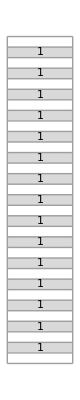
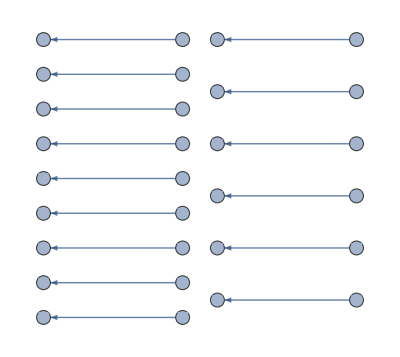
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
ssslin1=SSS[FromReducedRankIndex[2],"",30];
```

```mathematica
ssslin1[["Net"]]
```

{1→2,3→4,5→6,7→8,9→10,11→12,13→14,15→16,17→18,19→20,21→22,23→24,25→26,27→28,29→30}

```mathematica
ToNetDifferenceSets[ssslin1[["Net"]]]
```

{{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1}}

```mathematica
ReduceSetList@%
```

{€^14[{1},{}],{1}}

Use most compact part:

```mathematica
{€^14[{1},{}]}
```

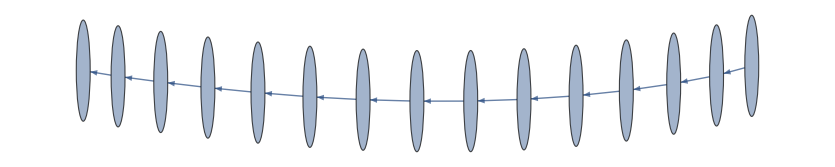
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
ssslin2=SSS[FromReducedRankIndex[4],"A",15,NetSize->550];
```

```mathematica
ssslin2[["Net"]]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15}

```mathematica
ToNetDifferenceSets[ssslin2[["Net"]]]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
ReduceSetList@%
```

{€^14[{1}]}

Note: pull up Jeanna Toulouse’s & Chris Trana’s posters, compare to their network summaries!

#### The 2D (mostly) hexagonal network

```mathematica
rsHex=FromReducedRankRuleSet[{"AA"->"BA","AB"->"AA","B"->"AA"}]
```

<|Index→1181262395,QCode→3243234232423,RuleSet→{AA→BA,AB→AA,B→AA}|>

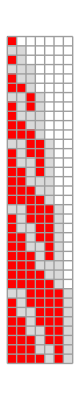
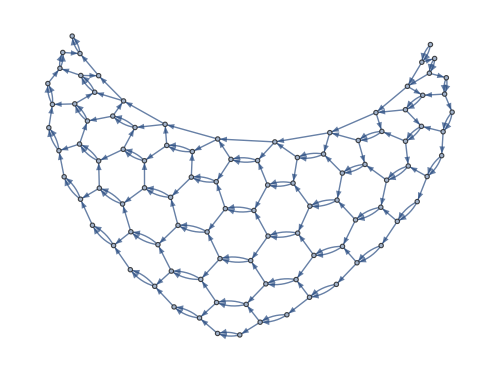
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sssHex=SSS[rsHex, "B",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->35,NetMax->100,NetSize->{500,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic];
```

```mathematica
SSSInteractiveDisplay[sssHex]
```

```mathematica
sssHex["Distance"]
```

{0,1,2,3,2,4,5,3,4,3,6,7,5,6,4,5,4,8,9,7,8,6,7,5,6,5,10,11,9,10,8,9,7,8,6,7,6,12,13,11,12,10,11,9,10,8,9,7,8,7,14,15,13,14,12,13,11,12,10,11,9,10,8,9,8,16,17,15,16,14,15,13,14,12,13,11,12,10,11,9,10,9,18,19,17,18,16,17,15,16,14,15,13,14,12,13,11,12,10,11,10,20,21,19,20,18,19,17,18,16,17,15,16,14,15,13,14,12,13,11,12,11,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,14,15,13,14,12,13,12,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,14,15,13,14,13,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,14,15,14,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,15,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,16,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,17,34,35,33,34,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,18,36,37,35,36,34,35,33,34,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,19,38,39,37,38,36,37,35,36,34,35,33,34,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21}

```mathematica
Tally[sssHex["Distance"]]
```

{{0,1},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,19},{21,19},{22,18},{23,17},{24,16},{25,15},{26,14},{27,13},{28,12},{29,11},{30,10},{31,9},{32,8},{33,7},{34,6},{35,5},{36,4},{37,3},{38,2},{39,1}}

```mathematica
Tally[sssHex["Distance"]][[1;;20]]
```

{{0,1},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19}}

```mathematica
Last/@%
```

{1,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

```mathematica
Accumulate[%]
```

{1,2,4,7,11,16,22,29,37,46,56,67,79,92,106,121,137,154,172,191}

```mathematica
NestList[Differences,%,2]//Grid
```

1 | 2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56 | 67 | 79 | 92 | 106 | 121 | 137 | 154 | 172 | 191
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |

```mathematica
ToNetDifferenceSets[sssHex["Net"]]
```

{{1,1},{1,3},{1,1},{1,2},{3,5},{1,1},{1,4},{1,1},{1,4},{5,7},{1,1},{1,6},{1,1},{1,6},{1,1},{1,6},{7,9},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{9,11},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{11,13},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{13,15},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{15,17},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{17,19},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{19,21},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{21,23},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{23,25},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{25,27},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{27,29},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{29,31},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{31,33},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{33,35},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{35,37},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{37},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1}}

```mathematica
ReduceSetList[%]
```

{€_(n$1⊨1)^2[{1,1},{1,4-n$1}],€_(n$1⊨1)^17[{1+2 n$1,3+2 n$1},€^(1+n$1)[{1,1},{1,2 (1+n$1)}]],{37},€^18[{1,1},{1}],{1,1}}

```mathematica
Position[%,37]
```

{{325,2},{362,1}}

```mathematica
%%[[1;;362]]
```

{{1,1},{1,3},{1,1},{1,2},{3,5},{1,1},{1,4},{1,1},{1,4},{5,7},{1,1},{1,6},{1,1},{1,6},{1,1},{1,6},{7,9},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{9,11},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{11,13},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{13,15},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{15,17},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{17,19},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{19,21},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{21,23},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{23,25},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{25,27},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{27,29},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{29,31},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{31,33},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{33,35},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{35,37},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{37}}

```mathematica
ReduceSetList[%]
```

{€_(n$1⊨1)^2[{1,1},{1,4-n$1}],€_(n$1⊨1)^17[{2 n$1+1,2 n$1+3},€^(n$1+1)[{1,1},{1,2 (n$1+1)}]],{37}}

```mathematica
%[[2]]/.n$1->k//InputForm
```

```mathematica
IndexedConcatenate[{1 + 2*k, 3 + 2*k}, IndexedConcatenate[{1, 1}, {1, 2*(1 + k)}, 1 + k], {k, 1, 17}]
```

€_(k⊨1)^17[{2 k+1,2 k+3},€^(k+1)[{1,1},{1,2 (k+1)}]]

```mathematica
IndexedConcatenate[{1 + 2 k, 3 + 2 k}, IndexedConcatenate[{1, 1}, {1, 2*(1 + k)}, 1 + k], {k, 0, 16}]
```

€_(k⊨0)^16[{2 k+1,2 k+3},€^(k+1)[{1,1},{1,2 (k+1)}]]

```mathematica
IndexedConcatenate[{-1 + 2 k, 1 + 2 k}, IndexedConcatenate[{1, 1}, {1, 2 k}, k], {k, 1, 17}]
```

€_(k⊨1)^17[{2 k-1,2 k+1},€^k[{1,1},{1,2 k}]]

```mathematica
{ExpandAll[%173]}=={ExpandAll[%176]}
```

True